```mathematica
m[δ_]=Integrate[Abs[ξ]Abs[ξ],{ξ,-δ,δ},Assumptions->{Element[δ,Reals],δ>0}];
θ[λ_,δ_]:=FullSimplify[3 Integrate[Abs[ξ](Abs[ξ]Abs[1+λ]-Abs[ξ]),{ξ,-δ,δ},Assumptions->{Element[δ,Reals]Element[λ,Reals],δ>0}]/m[δ]]
```

```mathematica
W[λ_]:=(1/2)k Power[θ[λ,δ],2]
```

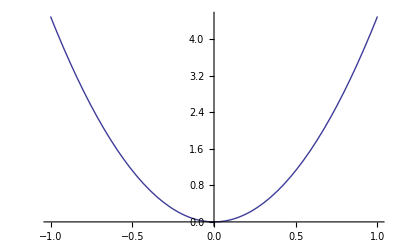

```mathematica
Plot[W[λ]/.k->1,{λ,-1,1}]
```

```mathematica
W[λ]
```

9/2 k (-1+Abs[1+λ])^2